```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
Print["Finished importing "<>file];
timestamps = Position[particles,"t"][[All,1]];
particlesT=Table[particles[[timestamps[[i]]+1;;timestamps[[i+1]]-1]],{i,Length[timestamps]-1}];
particlesT=Append[particlesT, particles[[timestamps[[-1]]+1;;]]];
nparticles=Length[particlesT[[1]]];
dt=particles[[timestamps[[2]],3]]-particles[[timestamps[[1]],3]];
{nparticles, dt,particlesT}
];
```

```mathematica
CCF[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
{np,dt,lt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,lt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
ld=Sqrt[rt[[1,1,3]]^2+rt[[1,1,4]]^2];
corrs=Table[{(j-i)*ld,
Cos[anglesT[[t,j]]-anglesT[[t,i]]]},{t,Ceiling[Length[rt]/2],Length[rt],ndc},
{i,Length[rt[[t]]]},
{j,i,Length[rt[[t]]]}];
gatheredCoors = Gather[Flatten[corrs,2],First[#1]==First[#2]&];
ccf=Table[Mean[gc],{gc,gatheredCoors}];
errs=Table[StandardDeviation[gatheredCoors[[i,All,2]]]/Sqrt[Length[gatheredCoors[[i]]]],{i,Length[gatheredCoors]}];
{ccf,errs}
];
```

```mathematica
nms=Table[ToString[i],{i,2,48}];
basedir="kbp04_nm";
dirs=Table[mdwlcl<>basedir<>s,{s,nms}];
```

```mathematica
kaps={".0001",".0004",".0007",".0010",".0040",".0070",".0100",".0400",".0700",".1000"};
basedir="nm50_kapb";
dirs=Table[mdwlcl<>basedir<>s,{s,kaps}];
```

```mathematica
seeds=Table[ToString[i],{i,2701,2750}];
basedir="nm50_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfs=Table[CCF[dr,10],{dr,dirs}];
```

```mathematica
nlms=Table[
NonlinearModelFit[
ccfs[[i,1,2;;]],
Exp[-x/(2Lp)],
{{Lp,10}},
x,
Weights->1/ccfs[[i,2,2;;]]^2
],
{i,1,Length[ccfs]}];
```

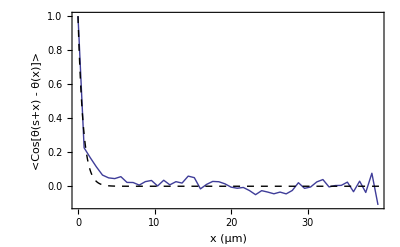
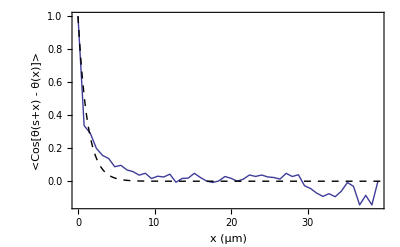
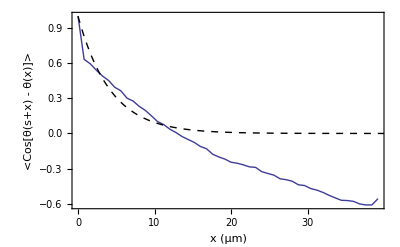
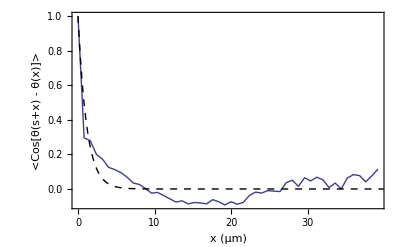
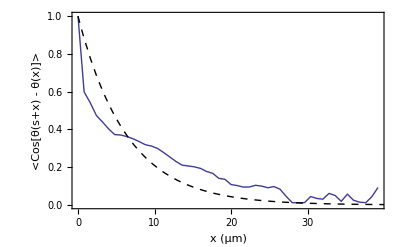
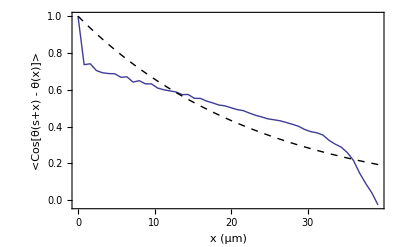
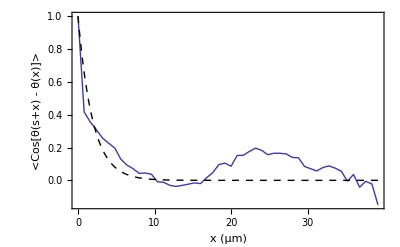
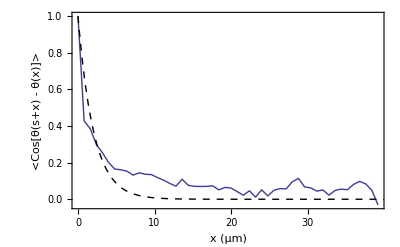

```mathematica
Table[
Show[
ListLinePlot[ccfs[[i,1]],Frame->True,
FrameLabel->{
"x (μm)", 
"<Cos[θ(s+x) - θ(x)]>",
"κ_input = .04\nκ_measured = "<>ToString[0.004*nlms[[i]]["ParameterTableEntries"][[1,1]]]
},PlotRange->Full
],
Plot[Normal[nlms[[i]]]/.x->l,{l,0,40},PlotRange->Full,PlotStyle->{Thick,Dashed,Black}]
],
{i,Length[nlms]}]
```

```mathematica
allLps=Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}];
```

```mathematica
Mean[allLps]
```

1.89943

```mathematica
StandardDeviation[allLps]
```

2.19804

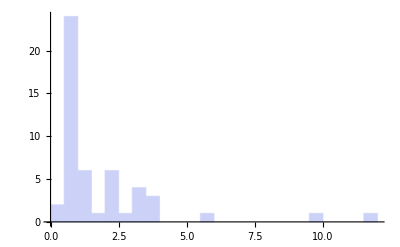

```mathematica
Histogram[allLps,20]
```

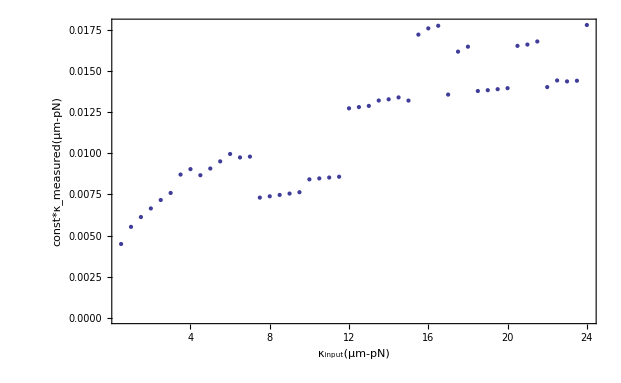

```mathematica
scale=(1.92-.04)/(nlms[[-1]]["ParameterTableEntries"][[1,1]]*.004-nlms[[1]]["ParameterTableEntries"][[1,1]]*.004);
kappakappa=Table[{ToExpression[kaps[[i]]],nlms[[i]]["ParameterTableEntries"][[1,1]]*.004},{i,Length[kaps]}];
ListPlot[kappakappa,Frame->True,FrameLabel->{"κ_input(μm-pN)","const*κ_measured(μm-pN)","Linear forcing springs"},PlotRange->Full,BaseStyle->{FontSize->16}]
```

```mathematica
LinearModelFit[kappakappa,x,x]
```

FittedModel[0.0057112+0.000476014 x]

```mathematica
1/.000476
```

2100.84

```mathematica
2100*.04
```

84.

```mathematica
0.4/0.011
```

36.3636

```mathematica
20*0.04
```

0.8

```mathematica
scale
```

416.

```mathematica
Table[{nlms[[i]]["ParameterTable"],seeds[[i]]},{i,Length[nlms]}]//TableForm
```

```mathematica
Histogram[Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}],100,Frame->True, FrameLabel->{"Lp(um)","counts","Distribution of persistence lengths as measured by CCF"},BaseStyle->{FontSize->16}]
```

```mathematica
pls=Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}];
```

```mathematica
Mean[pls]
```

64.7173

```mathematica
Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]
```

40

```mathematica
meanccfs=Total[ccfs[[All,1,1;;Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]]]]/Length[ccfs];
```

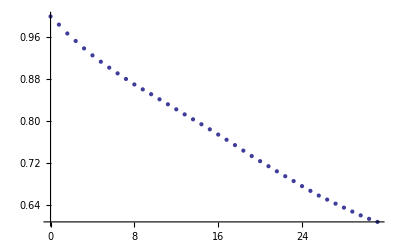

```mathematica
ListPlot[meanccfs]
```

```mathematica
nlm=NonlinearModelFit[
meanccfs,
Exp[-x/(2Lp)],
{Lp},
x];
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 30.7481 | 0.123067 | 249.849 | 4.11909×10^-64

```mathematica
Series[Cos[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
Series[Sqrt[1-x],{x,0,4}]
```

1-x/2-x^2/8-x^3/16-(5 x^4)/128+O[x]^5

```mathematica
FullSimplify[(1-Cos[θ/2])]
```

2 Sin[θ/4]^2

```mathematica
Series[1-2Cos[x/2]+Cos[x/2]^2,{x,0,6}]
```

x^4/64-x^6/1536+O[x]^7

```mathematica
Cos[π-x]
```

-Cos[x]

```mathematica
FullSimplify[1/2(1+Cos[θ])]
```

Cos[θ/2]^2